```mathematica
(** Model parameters are in SI units and are taken from Yuan et al., Adv. Mat. 1702884 (2018). **)
```

```mathematica
modelparameters0Sn={α1-> 3.02×10^5(T-78.3),α11->-2.26×10^8 ,α12-> -1.09×10^6(T-78.3)+221,α111->3.79×10^9, α112->1.13×10^9, α123->-1.89×10^9};
modelparameters3Sn={α1-> 2.83×10^5(T-66.5),α11->-2.59×10^8 ,α12-> -1.25×10^6(T-66.5)+222,α111->5.23×10^9, α112->1.75×10^9, α123->-2.36×10^9};
```

```mathematica
Clear[A]

A=α1 (P1^2+P2^2+P3^2)+α11 (P1^4+P2^4+P3^4)+α12((P1 P2)^2+(P1 P3)^2+(P2 P3)^2)+α111(P1^6+P2^6+P3^6)+α112(P1^2(P2^4+P3^4)+P2^2(P1^4+P3^4)+P3^2(P1^4+P2^4))+α123(P1^2 P2^2 P3^2);
```

```mathematica
D11=D[A,{P1,2}];
D22=D[A,{P2,2}];
D33=D[A,{P3,2}];
D12=D[D[A,P1],P2];
D13=D[D[A,P1],P3];
D23=D[D[A,P2],P3];
```

```mathematica
DMC={{D11,D12,D13},{D12,D22,D23},{D13,D23,D33}}/.{P1->0,P2->0,P3->0}//Simplify;
```

```mathematica
MatrixForm[DMC]
```

(2 α1 | 0 | 0
0 | 2 α1 | 0
0 | 0 | 2 α1)

```mathematica
Eigenvalues[DMC]//Simplify
```

{2 α1,2 α1,2 α1}

```mathematica
DMT={{D11,D12,D13},{D12,D22,D23},{D13,D23,D33}}/.{P1->0,P2->0,P3->Ps}//Simplify;
MatrixForm[DMT]
```

(2 (α1+Ps^4 α112+Ps^2 α12) | 0 | 0
0 | 2 (α1+Ps^4 α112+Ps^2 α12) | 0
0 | 0 | 2 (α1+6 Ps^2 α11+15 Ps^4 α111))

```mathematica
Eigenvalues[DMT]//Simplify
```

{2 (α1+6 Ps^2 α11+15 Ps^4 α111),2 (α1+Ps^4 α112+Ps^2 α12),2 (α1+Ps^4 α112+Ps^2 α12)}

```mathematica
AT=A/.{P1->0,P2->0,P3->Ps}//Simplify
```

Ps^2 (α1+Ps^2 α11+Ps^4 α111)

```mathematica
D[AT,Ps]/Ps/.Ps->√Ps2//Simplify
```

2 (α1+Ps2 (2 α11+3 Ps2 α111))

```mathematica
Solve[(α1+Ps2 (2 α11+3 Ps2 α111))==0,Ps2]
```

{{Ps2→(-α11-√(α11^2-3 α1 α111))/(3 α111)},{Ps2→(-α11+√(α11^2-3 α1 α111))/(3 α111)}}

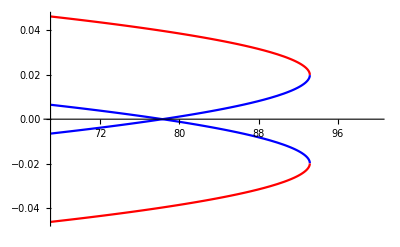

```mathematica
Plot[{(-α11+√(α11^2-3 α1 α111))/(3 α111)/.modelparameters0Sn,-(-α11+√(α11^2-3 α1 α111))/(3 α111)/.modelparameters0Sn,(-α11-√(α11^2-3 α1 α111))/(3 α111)/.modelparameters0Sn,-(-α11-√(α11^2-3 α1 α111))/(3 α111)/.modelparameters0Sn},{T,67,100},PlotStyle->{Blue,Blue,Red,Red}]
```

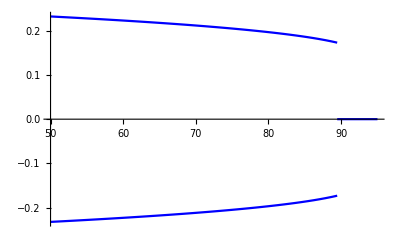

```mathematica
Show[Plot[{√((-α11+√(α11^2-3 α1 α111))/(3 α111))/.modelparameters0Sn,-√((-α11+√(α11^2-3 α1 α111))/(3 α111))/.modelparameters0Sn},{T,50,89.4561},PlotStyle->{Blue,Blue}],Plot[0,{T,89.4561,95},PlotStyle->Blue,PlotRange->All],PlotRange-> All]
```

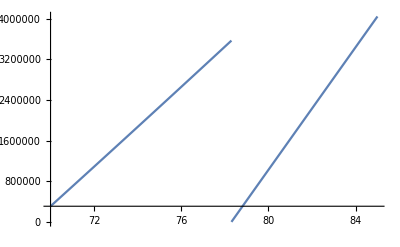

```mathematica
Show[Plot[(2 (α1+Ps^4 α112+Ps^2 α12))/.Ps->√((-α11+√(α11^2-3 α1 α111))/(3 α111))/.modelparameters0Sn, {T,70,78.3},PlotRange-> All],Plot[(2 α1)/.modelparameters0Sn,{T,78.3,85},PlotRange-> All],PlotRange-> All]
```

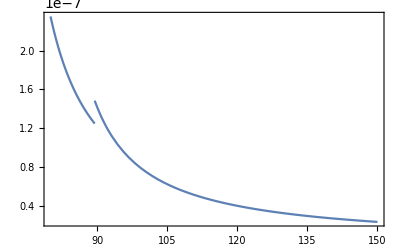

```mathematica
Show[Plot[(2 (α1+Ps^4 α112+Ps^2 α12))^-1/.Ps->√((-α11+√(α11^2-3 α1 α111))/(3 α111))/.modelparameters0Sn, {T,80,89.4561},PlotRange-> All],Plot[(2 α1)^-1/.modelparameters0Sn,{T,89.4561,150},PlotRange-> All],Frame->True]
```

```mathematica
FindRoot[AT==0/.Ps->√((-α11+√(α11^2-3 α1 α111))/(3 α111))/.modelparameters0Sn/.T->Tc,{Tc,89}]
```

{Tc→89.4561}

```mathematica
AT=A/.{P1->0,P2->0,P3->Ps}/.modelparameters0Sn//Simplify;
AO=A/.{P1->Ps/(√2),P2->Ps/(√2),P3->0}/.modelparameters0Sn//Simplify;
AR=A/.{P1->Ps/(√3),P2->Ps/(√3),P3->Ps/(√3)}/.modelparameters0Sn//Simplify;
```

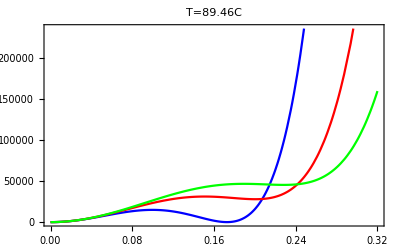

```mathematica
With[{T0=89.46},Plot[{AT/.T-> T0,AO/.T-> T0,AR/.T-> T0},{Ps,0.,0.32},Frame->True,PlotLabel->Style["T=89.46C",20],PlotStyle->{Blue,Red,Green}]]
```

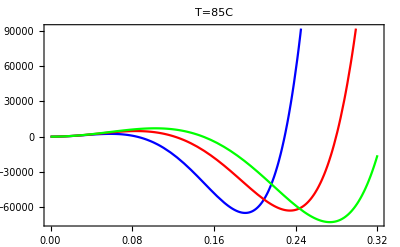

```mathematica
With[{T0=83},Plot[{AT/.T-> T0,AO/.T-> T0,AR/.T-> T0},{Ps,0.,0.32},Frame->True,PlotLabel->Style["T=85C",20],PlotStyle->{Blue,Red,Green}]]
```

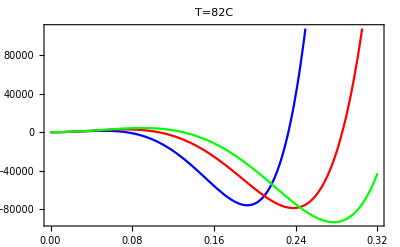

```mathematica
With[{T0=82},Plot[{AT/.T-> T0,AO/.T-> T0,AR/.T-> T0},{Ps,0.,0.32},Frame->True,PlotLabel->Style["T=82C",20],PlotStyle->{Blue,Red,Green}]]
```

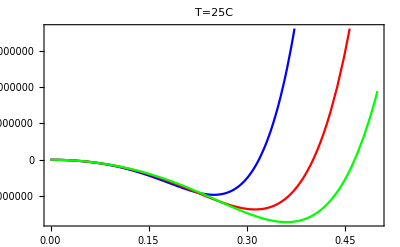

```mathematica
With[{T0=25},Plot[{AT/.T-> T0,AO/.T-> T0,AR/.T-> T0},{Ps,0.,0.5},Frame->True,PlotLabel->Style["T=25C",20],PlotStyle->{Blue,Red,Green}]]
```

## Experimental data

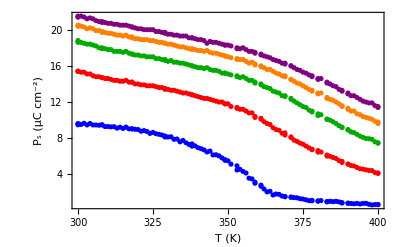

```mathematica
Clear[kv0, kv5,kv10,kv15,kv20]
kv0  = Import["C:\\PhD-Zipeng\\Research projects\\Gian-BZT\\Experiment data\\P(T)@E\\0.00.tab", "Table"];
kv0[[2;;All,{3,4}]]//TableView;
kv5 = Import["C:\\PhD-Zipeng\\Research projects\\Gian-BZT\\Experiment data\\P(T)@E\\470384.83.tab" ,"Table"];
kv5[[2;;All,{3,4}]]//TableView;
kv10 = Import["C:\\PhD-Zipeng\\Research projects\\Gian-BZT\\Experiment data\\P(T)@E\\1019167.13.tab","Table"];
kv10[[2;;All,{3,4}]]//TableView;
kv15 = Import["C:\\PhD-Zipeng\\Research projects\\Gian-BZT\\Experiment data\\P(T)@E\\1489551.96.tab","Table"];
kv15[[2;;All,{3,4}]]//TableView;
kv20 = Import["C:\\PhD-Zipeng\\Research projects\\Gian-BZT\\Experiment data\\P(T)@E\\1959936.79.tab","Table"];
kv20[[2;;All,{3,4}]]//TableView;

data0=ListPlot[kv0[[2;;All,{3,4}]]];
data5=ListPlot[kv5[[2;;All,{3,4}]]];
data10=ListPlot[kv10[[2;;All,{3,4}]]];
data15=ListPlot[kv15[[2;;All,{3,4}]]];
data20=ListPlot[kv20[[2;;All,{3,4}]]];

Show[ListPlot[kv0[[2;;All,{3,4}]],PlotStyle->Blue],ListPlot[kv5[[2;;All,{3,4}]],PlotStyle->Red],ListPlot[kv10[[2;;All,{3,4}]],PlotStyle->Darker[Green]],ListPlot[kv15[[2;;All,{3,4}]],PlotStyle->Orange],ListPlot[kv20[[2;;All,{3,4}]],PlotStyle->Purple],Frame-> True,FrameStyle-> Black,FrameLabel-> {Style["T (K)",{15,SingleLetterItalics->False}],Style["P_s (μC cm^-2)",15],None},PlotStyle->Automatic, PlotRange->All,FrameTicksStyle->Directive[15]]
```

## 2nd order fitting

## with (325.734,7.216*10^-3) (345.753,3.803*10^-3)

```mathematica
Clear[A,parameters]
Solve[{7.216*10^-3==(-b + √(b^2- 4c *7.83*10^5(325.734-365)))/(2c),3.803*10^-3==(-b + √(b^2- 4c *7.83*10^5(345.753-365)))/(2c)},{b,c}]
parameters= {T0-> 365, a-> 7.83×10^5, b->3.63078*10^9,c->8.72964*10^10,ρBaTiO3-> 6.02×10^3};
```

{{b→3.63078×10^9,c→8.72964×10^10}}

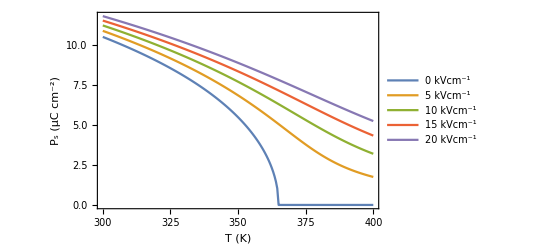

```mathematica
Clear[PsEqs,ΔSdata,ΔSTable,Psdata]

Tiin=300;Tfin=400;NoPin=200; 
(** Tiin=380;Tfin=430;NoPin=200; **)
E0Range=Range[0,20,5];
(**ΔE0Range={1.8,3.6,4.4,6.2,7.8};**)
ΔE0Range=Range[0,20,5];


PsEqs[E0_,T_]:=Ps/.FindRoot[-e0+b Ps^3+c Ps^5+a Ps (T-T0)/.parameters/.e0-> E0×10^5,{Ps,0.15,0.0,100}]//Quiet;
PsTable[E0_,Ti_,Tf_,NoP_]:=ParallelTable[{T,10^2 PsEqs[E0,T]},{T,Ti,Tf,(Tf-Ti)/NoP}];
ΔSTable[E0_,Ti_,Tf_,NoP_]:=ParallelTable[{T,-a/2 1/ρBaTiO3(PsEqs[0,T]^2-PsEqs[E0,T]^2)/.parameters},{T,Ti,Tf,(Tf-Ti)/NoP}];
Psdata=PsTable[#,Tiin,Tfin,NoPin]&/@E0Range;
ΔSdata= ΔSTable[#,Tiin,Tfin,NoPin]&/@ΔE0Range;
ListPlot[Psdata,Joined->True,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["T (K)",{15,SingleLetterItalics->False}],Style["P_s (μC cm^-2)",15],None},PlotLegends->{"0 kVcm^-1","5 kVcm^-1","10 kVcm^-1","15 kVcm^-1","20 kVcm^-1"},PlotStyle->Automatic, PlotRange->Automatic]

(*Export["C:\\PhD-Zipeng\\Research projects\\Gian-BZT\\Experiment data\\P(T)@E\\PT-simulated.csv",Psdata,"csv"]*)
```

{340,350,360,370,380}

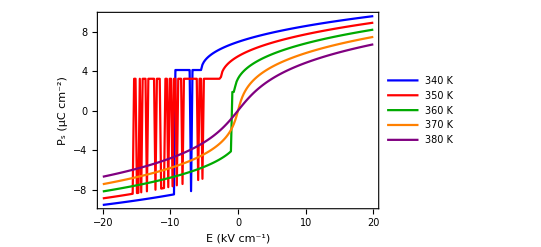

```mathematica
Clear[P,Ein,Efin,NuPin,PEEqs,PETable,PEdata, Eiin, Efin,NoPin]
Ein=-20;Efin=20;NuPin=190;
TRange=Range[340,380,10]
PEEqs[T_,E0_]:=P/.FindRoot[b P^3+c P^5+a P (T-T0)==E0*10^5/.parameters,{P,5}]//Quiet
PETable[T_,Ei_,Ef_,NuP_]:=ParallelTable[{E0,10^2 PEEqs[T,E0]},{E0,Ei,Ef,(Ef-Ei)/NuP}];
PEdata=PETable[#,Ein,Efin,NuPin]&/@TRange;
ListPlot[PEdata,Joined->True,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["E (kV cm^-1)",{15,SingleLetterItalics->False}],Style["P_s (μC cm^-2)",15],None},PlotLegends->{"340 K","350 K","360 K","370 K","380 K"},PlotStyle->{Blue,Red,Darker[Green], Orange,Purple,Darker[Yellow]},PlotRange-> Automatic]
```

{360,362,364,366,368,370}

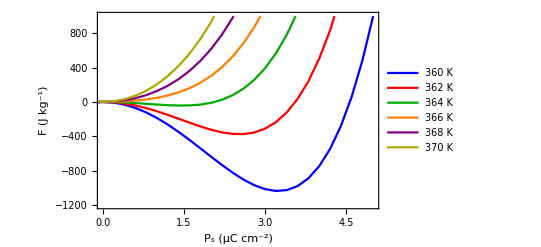

```mathematica
Pin=-0.2;Pfin=0.2;NuPin=200;
TRange=Range[360,370,2]
FEqs[T_,P_]:=(a(T-T0))/2 P^2+b/4 P^4+c/6 P^6/.parameters;
FTable[T_,Pi_,Pf_,NoP_]:=ParallelTable[{10^2 P,FEqs[T,P]},{P,Pi,Pf,(Pf-Pi)/NoP}];
Fdata=FTable[#,Pin,Pfin,NuPin]&/@TRange;
ListPlot[Fdata,Joined->True,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["P_s (μC cm^-2)",{15,SingleLetterItalics->False}],Style["F (J kg^-1)",15],None},PlotLegends->{"360 K","362 K","364 K","366 K","368 K","370 K"},PlotStyle->{Blue,Red,Darker[Green], Orange,Purple,Darker[Yellow]},PlotRange-> {{0,5},{-1200,1000}}]
```

## Comparison of experimental and theoretic data

OptionValue::nodef: Unknown option Joined for Graphics.

OptionValue::nodef: Unknown option PlotLegends for Graphics.

OptionValue::nodef: Unknown option PlotStyle for Graphics.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

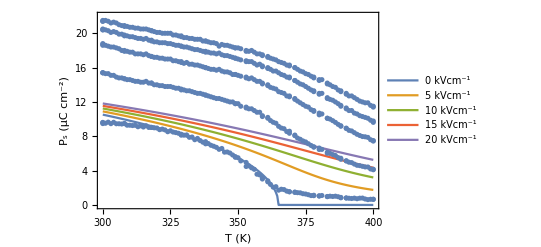

```mathematica
simu = ListPlot[Psdata,Joined->True,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["T (K)",{15,SingleLetterItalics->False}],Style["P_s (μC cm^-2)",15],None},PlotLegends->{"0 kVcm^-1","5 kVcm^-1","10 kVcm^-1","15 kVcm^-1","20 kVcm^-1"},PlotStyle->Automatic, PlotRange->Automatic];

Show[simu, data0,data5, data10,data15,data20, Joined->True,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["T (K)",{15,SingleLetterItalics->False}],Style["P_s (μC cm^-2)",15],None},PlotLegends->{"0 kVcm^-1","5 kVcm^-1","10 kVcm^-1","15 kVcm^-1","20 kVcm^-1"},PlotStyle->Automatic,PlotRange->{{300,400},{0,22}}]
```

### Low field comparison

{0,1,2,3,4,5}

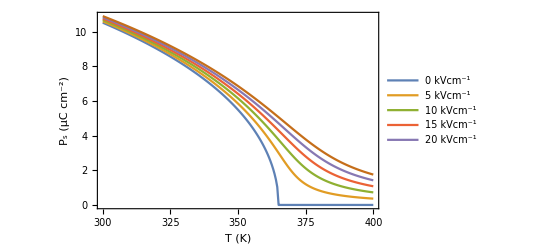

```mathematica
Clear[PsEqs,ΔSdata,ΔSTable,Psdata]

Tiin=300;Tfin=400;NoPin=200; 
(** Tiin=380;Tfin=430;NoPin=200; **)
E0Range=Range[0,5,1]
PsEqs[E0_,T_]:=Ps/.FindRoot[-e0+b Ps^3+c Ps^5+a Ps (T-T0)/.parameters/.e0-> E0×10^5,{Ps,0.15,0.0,100}]//Quiet;
PsTable[E0_,Ti_,Tf_,NoP_]:=ParallelTable[{T,10^2 PsEqs[E0,T]},{T,Ti,Tf,(Tf-Ti)/NoP}];
Psdata=PsTable[#,Tiin,Tfin,NoPin]&/@E0Range;
ListPlot[Psdata,Joined->True,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["T (K)",{15,SingleLetterItalics->False}],Style["P_s (μC cm^-2)",15],None},PlotLegends->{"0 kVcm^-1","5 kVcm^-1","10 kVcm^-1","15 kVcm^-1","20 kVcm^-1"},PlotStyle->Automatic, PlotRange->Automatic]
```

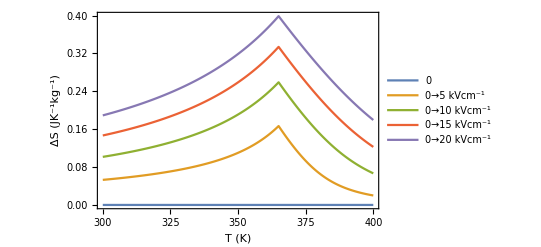

```mathematica
ListPlot[ΔSdata,Joined->True,PlotRange->All,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["T (K)",{15,SingleLetterItalics->False}],Style["ΔS (JK^-1kg^-1)",15],None},PlotStyle->Automatic,PlotLegends->{"0","0→5 kVcm^-1","0→10 kVcm^-1","0→15 kVcm^-1","0→20 kVcm^-1"}]
```

## 1st order fitting

```mathematica
Solve[{2.948*10^-4== -b/c,3.082*10^-3==(-b + √(b^2- 4c *7.83*10^5(349.13-365)))/(2c)},{b,c}]
```

{{b→-4.26447×10^8,c→1.44656×10^12}}

```mathematica
Solve[{2.948*10^-4== -b/c,2.244*10^-4==(-b + √(b^2- 4c *7.83*10^5(370.53-365)))/(2c)},{b,c}]
```

{{b→-8.08014×10^10,c→2.74089×10^14}}

```mathematica
Clear[A]
(**parameters= {T0-> 399.3,a-> 1.696×10^6,b-> -3.422×10^9,c-> 1.797×10^11,d-> 3.214×10^12,ρBaTiO3-> 6.02×10^3};**)
parameters= {T0-> 365, a-> 7.83×10^5, b->-4.264473306544202×10^8,c->1.4465648936717104×10^12};

A=(a(T-T0))/2 P^2+b/4 P^4+c/6 P^6-E0 P/.parameters;
```

```mathematica
1/Ps D[(a(T-T0))/2 P^2+b/4 P^4+c/6 P^6/.P-> Ps,{Ps,1}]//Simplify
```

b Ps^2+c Ps^4+a (T-T0)

## Zipeng’s fit, with (365,2.948*10^-4)(329.302,6.6032*10^-3)

```mathematica
Clear[A, parameters]
Solve[{2.948*10^-4== -b/c,6.6032*10^-3==(-b + √(b^2- 4c *7.83*10^5(329.302-365)))/(2c)},{b,c}]
parameters= {T0-> 365, a-> 7.83×10^5, b->1.97815×10^8,c->6.71015×10^11,ρBaTiO3-> 6.02×10^3};
```

{{b→-1.97815×10^8,c→6.71015×10^11}}

{0,5,10,15,20}

{0,5,10,15,20}

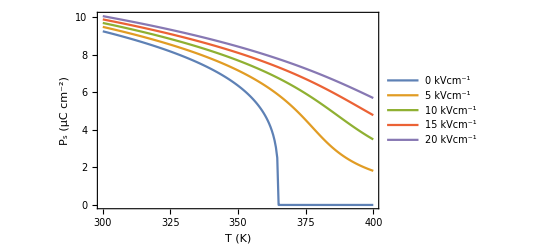

```mathematica
Clear[PsEqs,ΔSdata,ΔSTable,Psdata]

Tiin=300;Tfin=400;NoPin=200; 
(** Tiin=380;Tfin=430;NoPin=200; **)
E0Range=Range[0,20,5]
(**ΔE0Range={1.8,3.6,4.4,6.2,7.8};**)
ΔE0Range=Range[0,20,5]
PsEqs[E0_,T_]:=Ps/.FindRoot[-e0+b Ps^3+c Ps^5+a Ps (T-T0)/.parameters/.e0-> E0×10^5,{Ps,0.15,0.0,100}]//Quiet;
PsTable[E0_,Ti_,Tf_,NoP_]:=ParallelTable[{T,10^2 PsEqs[E0,T]},{T,Ti,Tf,(Tf-Ti)/NoP}];
ΔSTable[E0_,Ti_,Tf_,NoP_]:=ParallelTable[{T,-a/2 1/ρBaTiO3(PsEqs[0,T]^2-PsEqs[E0,T]^2)/.parameters},{T,Ti,Tf,(Tf-Ti)/NoP}];
Psdata=PsTable[#,Tiin,Tfin,NoPin]&/@E0Range;
ΔSdata= ΔSTable[#,Tiin,Tfin,NoPin]&/@ΔE0Range;
ListPlot[Psdata,Joined->True,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["T (K)",{15,SingleLetterItalics->False}],Style["P_s (μC cm^-2)",15],None},PlotLegends->{"0 kVcm^-1","5 kVcm^-1","10 kVcm^-1","15 kVcm^-1","20 kVcm^-1"},PlotStyle->Automatic]
```

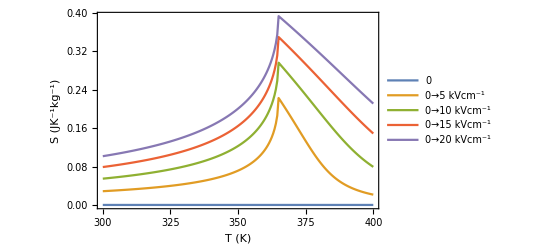

```mathematica
ListPlot[ΔSdata,Joined->True,PlotRange->All,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["T (K)",{15,SingleLetterItalics->False}],Style["S (JK^-1kg^-1)",15],None},PlotStyle->Automatic,PlotLegends->{"0","0→5 kVcm^-1","0→10 kVcm^-1","0→15 kVcm^-1","0→20 kVcm^-1"}]
```

## Zipeng's fit, with (365,2.948*10^-4) (349.13,3.082*10^-3)

```mathematica
Clear[A,parameters]
Solve[{2.948*10^-4== -b/c,3.082*10^-3==(-b + √(b^2- 4c *7.83*10^5(349.13-365)))/(2c)},{b,c}]
parameters= {T0-> 365, a-> 7.83×10^5, b->-4.26447*10^8,c->1.44656*10^12,ρBaTiO3-> 6.02×10^3};
```

{{b→-4.26447×10^8,c→1.44656×10^12}}

{0,5,10,15,20}

{0,5,10,15,20}

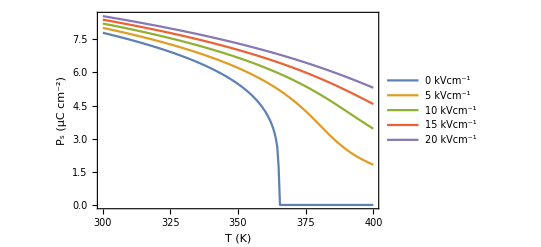

```mathematica
Clear[PsEqs,ΔSdata,ΔSTable,Psdata]

Tiin=300;Tfin=400;NoPin=200; 
(** Tiin=380;Tfin=430;NoPin=200; **)
E0Range=Range[0,20,5]
(**ΔE0Range={1.8,3.6,4.4,6.2,7.8};**)
ΔE0Range=Range[0,20,5]
PsEqs[E0_,T_]:=Ps/.FindRoot[-e0+b Ps^3+c Ps^5+a Ps (T-T0)/.parameters/.e0-> E0×10^5,{Ps,0.15,0.0,100}]//Quiet;
PsTable[E0_,Ti_,Tf_,NoP_]:=ParallelTable[{T,10^2 PsEqs[E0,T]},{T,Ti,Tf,(Tf-Ti)/NoP}];
ΔSTable[E0_,Ti_,Tf_,NoP_]:=ParallelTable[{T,-a/2 1/ρBaTiO3(PsEqs[0,T]^2-PsEqs[E0,T]^2)/.parameters},{T,Ti,Tf,(Tf-Ti)/NoP}];
Psdata=PsTable[#,Tiin,Tfin,NoPin]&/@E0Range;
ΔSdata= ΔSTable[#,Tiin,Tfin,NoPin]&/@ΔE0Range;
ListPlot[Psdata,Joined->True,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["T (K)",{15,SingleLetterItalics->False}],Style["P_s (μC cm^-2)",15],None},PlotLegends->{"0 kVcm^-1","5 kVcm^-1","10 kVcm^-1","15 kVcm^-1","20 kVcm^-1"},PlotStyle->Automatic]
```

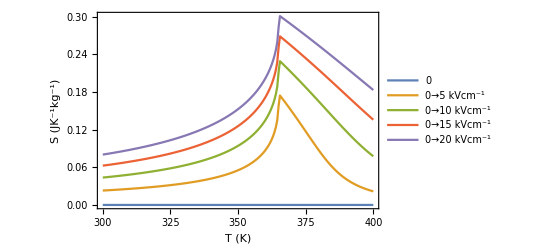

```mathematica
ListPlot[ΔSdata,Joined->True,PlotRange->All,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["T (K)",{15,SingleLetterItalics->False}],Style["S (JK^-1kg^-1)",15],None},PlotStyle->Automatic,PlotLegends->{"0","0→5 kVcm^-1","0→10 kVcm^-1","0→15 kVcm^-1","0→20 kVcm^-1"}]
```

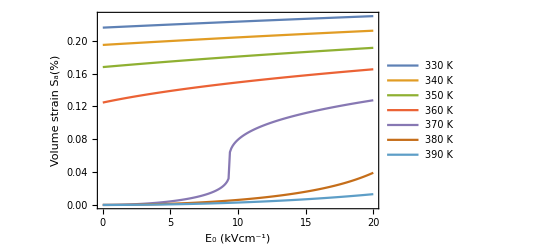

```mathematica
Clear[strain]

E0in=0;E0fin=20;NoPin=200; 
temperatures=Range[330,390,10];
straintable[T_,E0i_,E0f_,NoP_]:=ParallelTable[{E0,10×Ps^2/.FindRoot[-e0+b Ps^3+c Ps^5+d Ps^7+a Ps (T-T0)/.parameters/.e0-> E0×10^5,{Ps,0.15,-100,100}]//Quiet},{E0,E0i,E0f,(E0f-E0i)/NoP}];
straindata=straintable[#,E0in,E0fin,NoPin]&/@temperatures;
ListPlot[straindata,Joined->True,Frame->True,FrameTicksStyle->Directive[15],FrameStyle-> Black,FrameLabel-> {Style["E_0 (kVcm^-1)",{15,SingleLetterItalics->False}],Style["Volume strain S_a(%)",15],None},PlotLegends->{"330 K","340 K","350 K","360 K","370 K","380 K","390 K"}]
```

```mathematica
(*change a by Curie Weiss fitting*)
```